```mathematica
SetDirectory["C:\\Users\\HILL\\Documents\\GitHub\\thesis\\figures"];
```

```mathematica
data=Import["jitter\\low_jitter.csv"];
```

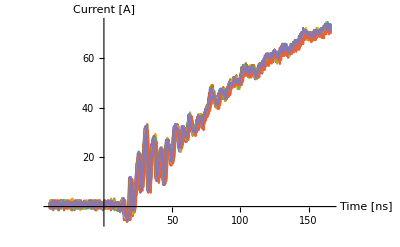

```mathematica
ListLinePlot[Table[
Thread[{data⟦All,1⟧,data⟦All,j⟧
}],{j,2,21}],PlotStyle->Automatic,
TicksStyle->Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],
AxesStyle->{{Black,Thick},{Black,Thick}},
AxesLabel->{Style["Time [ns]",Black,FontSize->fontsize],Style["Current [A]",Black,FontSize->fontsize]},
Ticks->{
{{5.*^-8,50,tick,Directive[Thick]},
{1*^-7,100,tick,Directive[Thick]},
{1.5*^-7,150,tick,Directive[Thick]}},
{{2,20,tick,Directive[Thick]},{4,40,tick,Directive[Thick]},{6,60,tick,Directive[Thick]}}
},ImageSize->Full]
```

```mathematica
tick=0.04;fontsize=44;
```

```mathematica
Quantity[5*^-8,"Seconds"]
```

1/20000000 s

```mathematica
Ticks->{
```

```mathematica
UnitConvert[Quantity[1/20000000,"Seconds"],"Nanoseconds"]
```

50 ns

```mathematica
QuantityMagnitude[Quantity[1/20000000,"Seconds"]]
```

1/20000000

```mathematica
N[1/20000000]
```

5.×10^-8

```mathematica
Ticks->{{{-12.5*^-9,-12.5,0.08,Directive[Thick]},{0,0},{12.5*^-9,12.5,0.08,Directive[Thick]},{25*^-9,25,0.08,Directive[Thick]},{37.5*^-9,37.5,0.08,Directive[Thick]},{50*^-9,50,0.08,Directive[Thick]},{62.5*^-9,62.5,0.08,Directive[Thick]},{75*^-9,75,0.08,Directive[Thick]},{87.5*^-9,87.5,0.08,Directive[Thick]}},None}
```

Ticks→{{{-1.25×10^-8,-12.5,0.08,Directive[Thickness[Large]]},{0,0},{1.25×10^-8,12.5,0.08,Directive[Thickness[Large]]},{1/40000000,25,0.08,Directive[Thickness[Large]]},{3.75×10^-8,37.5,0.08,Directive[Thickness[Large]]},{1/20000000,50,0.08,Directive[Thickness[Large]]},{6.25×10^-8,62.5,0.08,Directive[Thickness[Large]]},{3/40000000,75,0.08,Directive[Thickness[Large]]},{8.75×10^-8,87.5,0.08,Directive[Thickness[Large]]}},None}

```mathematica
ListPlot[datasetsingle[[80;;600]],Joined->True,PlotStyle->{Thickness[0.005]},PlotRange->All,
TicksStyle->{Directive[Black,Large,FontFamily->"Helvetica"],Directive[Red,Bold]},
Ticks->{{{-12.5*^-9,-12.5,0.08,Directive[Thick]},{0,0},{12.5*^-9,12.5,0.08,Directive[Thick]},{25*^-9,25,0.08,Directive[Thick]},{37.5*^-9,37.5,0.08,Directive[Thick]},{50*^-9,50,0.08,Directive[Thick]},{62.5*^-9,62.5,0.08,Directive[Thick]},{75*^-9,75,0.08,Directive[Thick]},{87.5*^-9,87.5,0.08,Directive[Thick]}},None},AxesStyle->Thick,AxesLabel->{Style["Time [ns]",Small,Black,FontFamily->"Helvetica",FontSize->30],Style["Voltage [V]",Black,FontFamily->"Helvetica",FontSize->30]}]
```